```mathematica
μ = Quantity[100,"Kilograms"]
```

100 kg

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[R, e]]
```

```mathematica
Subscript[R, e]= Quantity[6378.1*^3,"Meters"]
```

6.3781×10^6 m

```mathematica
3*Subscript[R, e]
```

1.91343×10^7 m

```mathematica
Symbolize[Subscript[R, 0]]
```

```mathematica
Subscript[R, 0] = 3*Subscript[R, e]
```

1.91343×10^7 m

```mathematica
Symbolize[Subscript[M, e]]
```

```mathematica
Subscript[M, e] = Quantity[5.972*^24 , "Kilograms"]
```

5.972×10^24 kg

```mathematica
G= UnitConvert[Quantity[1,"GravitationalConstant"]]
```

6.674×10^-11 m^3/(kg s^2)

```mathematica
Symbolize[Subscript[l, scale]]
```

```mathematica
Subscript[l, scale] = 0.5
```

0.5

```mathematica
l = μ*Subscript[R, 0] * Sqrt[G*Subscript[M, e]/Subscript[R, 0]]*Subscript[l, scale]
```

4.36656×10^12 kg m^2/s

```mathematica
Symbolize[Subscript[v, r,0]]
```

```mathematica
Symbolize[Subscript[v, t,0]]
```

```mathematica
Subscript[v, r,0] = Quantity[500,"Meters"/"Seconds"]
```

500 m/s

```mathematica
Subscript[v, t,0] = Sqrt[G*Subscript[M, e]/Subscript[R, 0]]*Subscript[l, scale]
```

2282.06 m/s

```mathematica
Symbolize[Subscript[E, t]]
```

```mathematica
Subscript[E, t] = (1/2)*μ*(Subscript[v, t,0]^2 + Subscript[v, r,0]^2) - G*Subscript[M, e]*μ/Subscript[R, 0]
```

-1.81022×10^9 kg m^2/s^2

```mathematica
Subscript[E, t] + G*Subscript[M, e]*μ/Subscript[R, 0] - l^2/(2*μ*Subscript[R, 0]^2)
```

1.25×10^7 kg m^2/s^2

```mathematica
r = Quantity["Meters"]
```

1 m

```mathematica
f[r_]:= Subscript[R, 0]*(l/r^2)/Sqrt[2*μ*(Subscript[E, t] + G*Subscript[M, e]*μ/r - l^2/(2*μ*r^2))]
```

```mathematica
f[Subscript[R, 0]]
```

4.56411

```mathematica
Subscript[R, 0]
```

1.91343×10^7 m

```mathematica
g[x_]:= Subscript[R, 0]*(l/Quantity[x,"Meters"]^2)/Sqrt[2*μ*(Subscript[E, t] + G*Subscript[M, e]*μ/Quantity[x,"Meters"] - l^2/(2*μ*Quantity[x,"Meters"]^2))]
```

```mathematica
g[8*^9]
```

0.-2.17264×10^-6 ⅈ

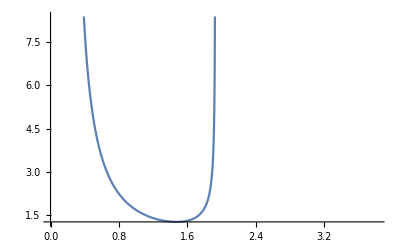

```mathematica
Plot[g[x],{x,0*QuantityMagnitude@Subscript[R, 0],2*QuantityMagnitude@Subscript[R, 0]}]
```

```mathematica
d[x_]:=(-1/Subscript[E, t])*(Subscript[E, t] + G*Subscript[M, e]*μ/Quantity[x,"Meters"] - l^2/(2*μ*Quantity[x,"Meters"]^2))
```

```mathematica
d[1*QuantityMagnitude@Subscript[R, 0]]
```

0.00690522

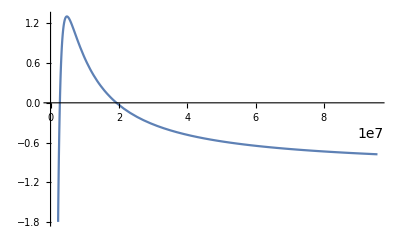

```mathematica
Plot[d[x],{x,0*QuantityMagnitude@Subscript[R, 0],5*QuantityMagnitude@Subscript[R, 0]}]
```

```mathematica
r1=First[Quantity[FindRoot[d,{0.001*QuantityMagnitude@Subscript[R, 0],1*QuantityMagnitude@Subscript[R, 0]}],"Meters"]/Subscript[R, 0]]
```

0.142694

```mathematica
r2=First[Quantity[FindRoot[d,{2*QuantityMagnitude@Subscript[R, 0],5*QuantityMagnitude@Subscript[R, 0]}],"Meters"]/Subscript[R, 0]]
```

1.00805

```mathematica
θ[r_]:= Integrate[g[x]/(QuantityMagnitude@Subscript[R, 0]),{x,r1*QuantityMagnitude@Subscript[R, 0],r}]
```

```mathematica
θ[1.0*QuantityMagnitude@Subscript[R, 0]]
```

3.06869

```mathematica
r2*QuantityMagnitude@Subscript[R, 0]
```

1.92884×10^7

```mathematica
a = Quantity[FindRoot[θ[r]-1.0,{r,((r1+r2)/2)*QuantityMagnitude@Subscript[R, 0]}],"Meters"]
```

FindRoot::nlnum: The function value {Undefined} is not a list of numbers with dimensions {1} at {r} = {-6.84927×10^6}.

{(1 m→1.10094×10^7) m}

```mathematica
QuantityMagnitude@a
```

{1 m→1.10094×10^7}

```mathematica
((r2+r1)/2)*QuantityMagnitude@Subscript[R, 0]
```

1.10094×10^7

```mathematica
θ[2.730354844167488*^6]
```

0

```mathematica
inv[θ_,R_]:=Function[{t},R/. FindRoot[θ-t,{R,r2*0.9999999*QuantityMagnitude@Subscript[R, 0]}]]
```

```mathematica
thetinv=inv[θ[x],x]
```

Function[{t$},x/.FindRoot[ConditionalExpression[3.08762×10^11 (5.0874×10^-12+3.23874×10^-12 ArcSin[1.32979-(6.36116×10^6)/x]), 2.×10^-14<Re[x]≤1.9288418388081897516×10^7||x∉ℝ]-t$,{x,r2 1. QuantityMagnitude[R_0]}]]

```mathematica
thetinv[1.0]
```

FindRoot::nlnum: The function value {Undefined} is not a list of numbers with dimensions {1} at {x} = {-1.04905×10^7}.

1.51773×10^7

```mathematica
θ[0.9999999*r2*QuantityMagnitude@Subscript[R, 0]]
```

3.14134

```mathematica
invthet=Interpolation[Table[{θ[r],r},{r,r1*QuantityMagnitude@Subscript[R, 0],0.9999999*r2*QuantityMagnitude@Subscript[R, 0],1*^7}]]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

InterpolatingFunction[…]

```mathematica
θ[3*^6]
```

0.659017

```mathematica
{x,3*^6,1.8*^7,1*^6}
```

{x,3000000,1.8×10^7,1000000}

```mathematica
Table[{θ[r],r},{r,3*^6,1.8*^7,1*^6}]
```

{{0.659017,3000000},{1.30726,4000000},{1.62839,5000000},{1.84377,6000000},{2.0054,7000000},{2.13489,8000000},{2.24336,9000000},{2.33738,10000000},{2.42114,11000000},{2.49758,12000000},{2.56895,13000000},{2.63711,14000000},{2.70386,15000000},{2.77129,16000000},{2.84251,17000000},{2.92388,18000000}}

```mathematica
θ[3*^6]
```

0.659017

```mathematica
invthet = Interpolation[Table[{θ[r],r},{r,3*^6,1.8*^7,1*^5}]]
```

InterpolatingFunction[…]

```mathematica
invthetother = Interpolation[Table[{-θ[r],r},{r,3*^6,1.8*^7,1*^5}]]
```

InterpolatingFunction[…]

```mathematica
invthetother[2.0]
```

InterpolatingFunction::dmval: Input value {2.} lies outside the range of data in the interpolating function. Extrapolation will be used.

-53198.9

InterpolatingFunction::dmval: Input value {0.0000641141} lies outside the range of data in the interpolating function. Extrapolation will be used.

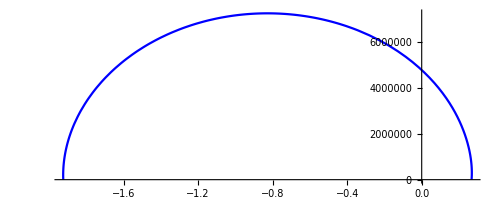

```mathematica
top =PolarPlot[invthet[x],{x,0,π},PlotStyle->{Blue,Dashing[None]}]
```

InterpolatingFunction::dmval: Input value {-3.14153} lies outside the range of data in the interpolating function. Extrapolation will be used.

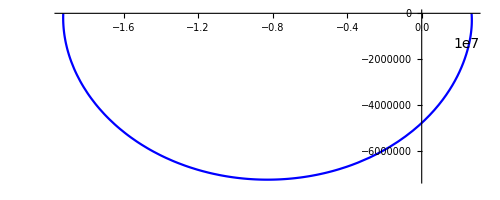

```mathematica
bottom = PolarPlot[invthetother[x],{x,-Pi,0},PlotStyle->{Blue,Dashing[None]}]
```

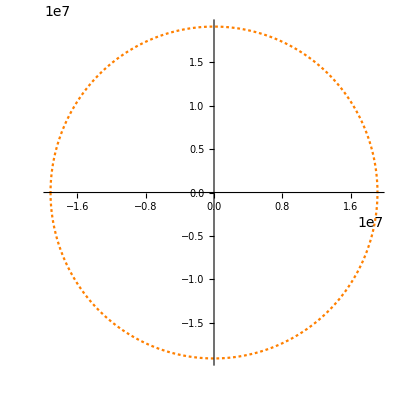

```mathematica
start = PolarPlot[Subscript[R, 0],{x,-Pi,Pi},PlotStyle->{Orange,Dashing[Tiny]}]
```

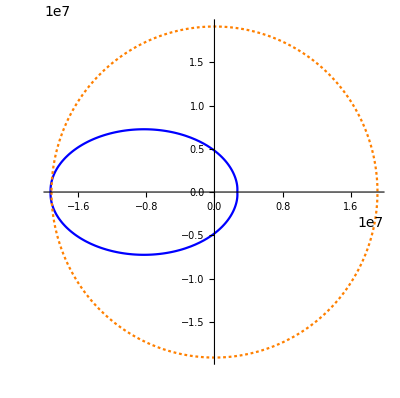

```mathematica
Show[top,bottom,start,PlotRange->All]
```